```mathematica
Clear["Global`*"]
SetOptions[{ContourPlot,Plot3D,ParametricPlot,Plot,ListLinePlot,ListPlot},BaseStyle->{FontFamily->"Palatino",FontSize->20},ImageSize->600,PlotRange->All];
SetOptions[{ParametricPlot,Plot,ListLinePlot,ListPlot},PlotStyle->(Directive[AbsoluteThickness[3],#]&/@ColorData[68,"ColorList"]),Frame->False,FrameStyle-> Thickness[0.002]];
```

{{e1→0.392375},{e1→1.27429}}

{0.264076}

0.16

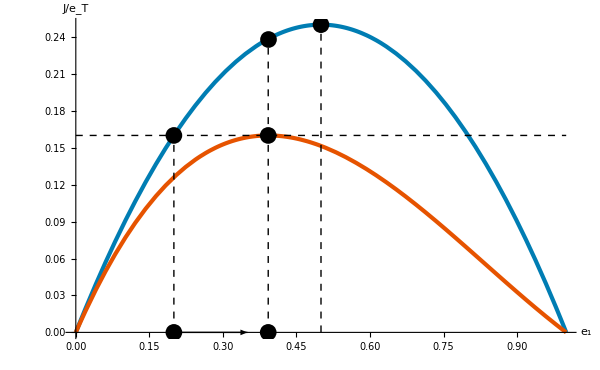

/Users/rplanque/Documents/SystemsBiology/qORAC2/qORAC_control.jpg

```mathematica
f1=e1(1-e1);
f2=e1(e1-1)(e1-1.5);
sols=Solve[D[f2,e1]==0,e1]
heightatmax=f2/.{sols[[1]]}
actualheight=f1/.{e1->0.2}
predictedheight = f1/.sols[[1]];
factor=actualheight/heightatmax;

p1=Plot[{e1(1-e1),factor e1(e1-1)(e1-1.5)},{e1,0,1},Axes->{True,True},AxesLabel->{"e_1","J/e_T"}];
p2=Graphics[{PointSize[0.02],Black,Point[{0.2,actualheight}]}];
p3=Graphics[{PointSize[0.02],Black,Point[{e1/.sols[[1]],actualheight}]}];
p4=Graphics[{Dashed,Black,Line[{{0,actualheight},{1,actualheight}}]}];
p5=Graphics[{PointSize[0.02],Black,Point[{1/2,f1/.{e1->1/2}}](*,Text["(J(SuperscriptBox[e, opt]; SubscriptBox[x, 0]))/((e^opt)_T)",{1/2+0.02,(f1/.{e1->1/2})+0.02}]*)}];
p6=Graphics[{PointSize[0.02],Black,Point[{0.2,0}](*,Text["J(e(t);x_0)/e(t)_T",{0.2+0.02,0.02}]*)}];
p7=Graphics[{PointSize[0.02],Black,Point[{e1/.sols[[1]],0}]}];
p8=Graphics[{Dashed,Black,Line[{{0.2,0},{0.2,actualheight}}]}];

p9=Graphics[{Dashed,Black,Line[{{1/2,0},{1/2,1/4}}]}];
p10=Graphics[{Dashed,Black,Line[{{e1/.sols[[1]],0},{e1/.sols[[1]],predictedheight}}]}];
p11=Graphics[Arrow[{{0.2,0},{0.35,0}}]];
p12=Graphics[{PointSize[0.02],Black,Point[{e1/.sols[[1]],predictedheight}]}];

Show[p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,p11,p12]
Export["/Users/rplanque/Documents/SystemsBiology/qORAC2/qORAC_control.jpg",Show[p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,p11,p12],ImageResolution->300]
```